Solving for Electric Potential of an infinitely long, hollow prism, with metallic walls and a square cross-section, with square metallic inner conductor of unit potential. Using relaxation method.

```mathematica
ClearAll["Global`*"]
```

```mathematica
Lsqr=1; (*the outer square side length*)
Ssqr=0.2; (*the inner square side lenght*)
dx = 0.2; (*the step*)
v=Table[0,{i,-Lsqr,Lsqr,dx},{j,-Lsqr,Lsqr,dx}]; (*initialization of potential*)
v[[All,1]]=0;
v[[All,-1]]=0;
v[[1,All]]=0;
v[[-1,All]]=0;
Do[v[[i,j]]=1,
{i,Lsqr/dx-Ssqr/dx+1,Lsqr/dx+Ssqr/dx+1},{j,Lsqr/dx-Ssqr/dx+1,Lsqr/dx+Ssqr/dx+1}
]
(*the boundry potential conditions*)
```

```mathematica
(*Begin Relaxation method*)
tol = 0.00000001; (*tolerance*)
cond = 0; (*the condition to continue relaxation process*)
lx=Length[Range[-1,1,dx]]; (*the spatial parameter*)
vo = v; (*initial potential guess*)
counter = 0;
While[cond==0, Do[
Do[
(*Fix the Boundry condition every time*)
v[[All,1]]=0;
v[[All,-1]]=0;
v[[1,All]]=0;
v[[-1,All]]=0;
Do[v[[i,j]]=1,
{i,Lsqr/dx-Ssqr/dx+1,Lsqr/dx+Ssqr/dx+1},{j,Lsqr/dx-Ssqr/dx+1,Lsqr/dx+Ssqr/dx+1}
];
(*Solving Labace for better estimation*)
v[[i,j]]=0.25(v[[i+1,j]]+v[[i-1,j]]+v[[i,j+1]]+v[[i,j-1]]),{j,2,2*(Lsqr/dx)}]
,{i,2,2*(Lsqr/dx)}]; 
(*repeat if condition and tolerance does not satisfied*)
dv = Abs[v-vo];
If[Max[dv]< tol,cond = 1]; vo = v;counter++];
```

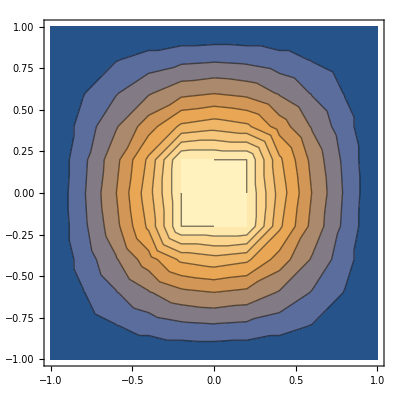

```mathematica
(*the potential contour plot*)
ListContourPlot[v,DataRange->{{-1,1},{-1,1}}]
```

```mathematica
(*the Potential 3d Plot*)
ListPlot3D[v,DataRange->{{-1,1},{-1,1}}]
```

-Graphics3D-

```mathematica
(*Electric field*)
Ex=v;
Ey=v;
Do[Do[Ex[[i,j]]=-(1/dx)(v[[i+1,j]]-v[[i-1,j]]),{j,2,lx-1}]
,{i,2,lx-1}]; 
Do[Do[Ey[[i,j]]=-(1/dx)(v[[i,j+1]]-v[[i,j-1]]),{j,2,lx-1}]
,{i,2,lx-1}];
```

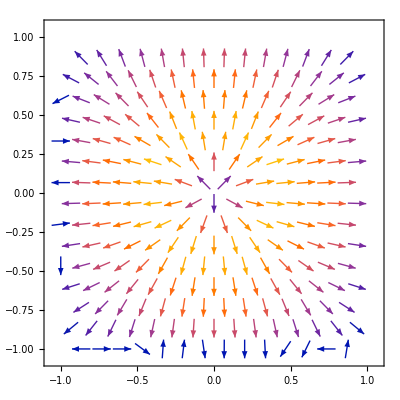

```mathematica
(*Electric field plot*)
ExEy=Table[{Ex[[i,j]],Ey[[i,j]]},{i,lx},{j,lx}];
ListVectorPlot[ExEy,DataRange->{{-1,1},{-1,1}}]
```

-----------------------------------------------------------------------------

Solving for Electric Potential of parallel capacitor plates at V=-1,+1, put inside a metallic square (to have boundaries of our problem). Using relaxation method.

```mathematica
ClearAll["Global`*"]
```

```mathematica
Lsqr=1; (*the Large square side lenght*)
pplate=0.4; (*the positive plate distance from origin*)
lplate=0.4; (*the Nigatitive plate distance from origin*)
dx = 0.2;
v=Table[0,{i,-Lsqr,Lsqr,dx},{j,-Lsqr,Lsqr,dx}]; (*initializing potential*)
(*Outer square Boundary cond.*)
v[[All,1]]=0;
v[[All,-1]]=0;
v[[1,All]]=0;
v[[-1,All]]=0;
(*Outer Plates Boundary cond.*)
Do[v[[j,Lsqr/dx-pplate/dx+1]]=1,{j,Lsqr/dx-lplate/dx+1,Lsqr/dx+lplate/dx+1}
]
Do[v[[j,Lsqr/dx+pplate/dx+1]]=-1,{j,Lsqr/dx-lplate/dx+1,Lsqr/dx+lplate/dx+1}
]
```

```mathematica
(*Solving Potential by relaxation method*)
tol = 0.00000001;
cond = 0;
lx=Length[Range[-1,1,dx]];
vo = v;
counter = 0;
(*Begin Relaxation method*)
While[cond==0, Do[
Do[
Do[
(*Fix the Boundry condition every time*)
v[[All,1]]=0;
v[[All,-1]]=0;
v[[1,All]]=0;
v[[-1,All]]=0;
v[[j,Lsqr/dx-pplate/dx+1]]=1,{j,Lsqr/dx-lplate/dx+1,Lsqr/dx+lplate/dx+1}
];
Do[v[[j,Lsqr/dx+pplate/dx+1]]=-1,{j,Lsqr/dx-lplate/dx+1,Lsqr/dx+lplate/dx+1}
];
(*Solving Labace for better estimation*)v[[i,j]]=0.25(v[[i+1,j]]+v[[i-1,j]]+v[[i,j+1]]+v[[i,j-1]]),{j,2,2*(Lsqr/dx)}]
,{i,2,2*(Lsqr/dx)}]; 
(*repeat if condition and tolerance does not satisfied*)
dv = Abs[v-vo];
If[Max[dv]< tol,cond = 1]; vo = v;counter++];
```

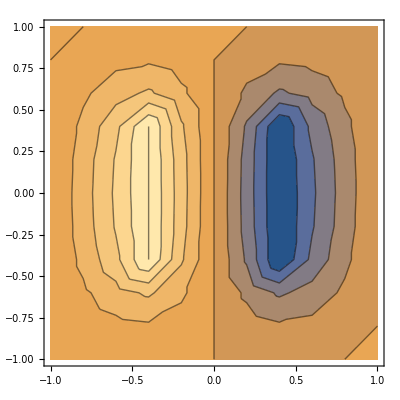

```mathematica
(*Potential contour plot*)
ListContourPlot[v,DataRange->{{-1,1},{-1,1}}]
```

```mathematica
(*Potential 3d Plot*)
ListPlot3D[v,DataRange->{{-1,1},{-1,1}}]
```

-Graphics3D-

```mathematica
(*Electric Feild*)
Ex=v;
Ey=v;
Do[Do[Ex[[i,j]]=-(1/dx)(v[[i+1,j]]-v[[i-1,j]]),{j,2,lx-1}]
,{i,2,lx-1}]; 
Do[Do[Ey[[i,j]]=-(1/dx)(v[[i,j+1]]-v[[i,j-1]]),{j,2,lx-1}]
,{i,2,lx-1}];
```

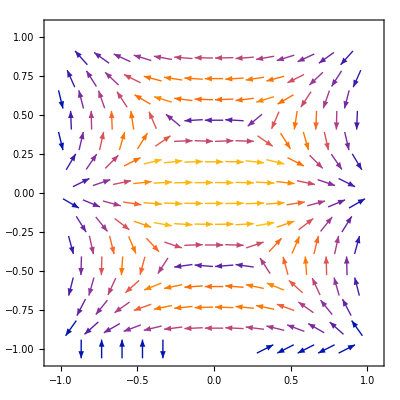

```mathematica
(*Electric Field Plot*)
ExEy=Table[{Ey[[i,j]],Ex[[i,j]]},{i,lx},{j,lx}];
ListVectorPlot[ExEy,DataRange->{{-1,1},{-1,1}}]
```